## Figure: Transient simulations of Fussmann predator-prey model

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/hopf_fussmann_2000/model"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0.1;
bh=0.16;
```

## Import data

```mathematica
dirName="ews_trans_lowhopf2";
dataDir="data_export/"<>dirName;
```

```mathematica
(* Import original EWS *)
ewsSingles=Import[dataDir<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum data *)
specSingles=Import[dataDir<>"/pspecs.csv"];
```

```mathematica
(* Import Kendall tau values *)
ktauData=Import[dataDir<>"/ktau.csv"];
```

```mathematica
(* AIC values at t=300 *)
aicData=Import[dataDir<>"/aic_t300.csv"];
```

## Figure Params

```mathematica
stateVar="Chlorella";
```

```mathematica
(* number of ews trajectories to show *)
numEws=5;
```

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ltb=0.001; (* bifurcation line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
plotNum=3;
```

```mathematica
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,Smax,AIC fold,AIC hopf,AIC null,Params fold,Params flip,Params hopf,Params null}

```mathematica
(* Extract time info *)
tVals=Cases[
ewsSingles[[2;;,{1,2,3}]],
{1,stateVar,_}][[;;,3]];
```

```mathematica
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
```

```mathematica
(* Number of realisations *)
Union[ewsSingles[[2;;,1]]]
```

{1,2,3,4,5}

```mathematica
(* Extract trajectory data *)
dfTraj=Table[
Cases[
ewsSingles[[2;;,{1,2,3,4}]],
{i,stateVar,_,_}]⟦;;,{3,4}⟧,
{i,1,5}];
```

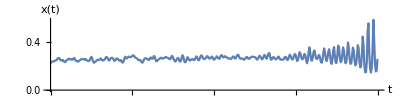

```mathematica
(* plot of x variable in time *)
plotX = ListPlot[dfTraj[[plotNum]],
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
AxesLabel->{"t","x(t)"},
PlotRange->{All,All}]
```

## Bifurcation diagram

```mathematica
bifPtsChlor=Import["../data/bifPtsChlor.mat"];
```

```mathematica
(* functions to turn bifurcation coordinates to time coordinates *)
bifToTime[list_ ]:=(list-bl)*tmax /(bh-bl)
```

```mathematica
(* Scale bifPtsChlor and have as a function of time instead of bif parameter *)
bifPtsChlorScaled=Table[Table[{bifToTime[bifPtsChlor[[j,i,1]]],bifPtsChlor[[j,i,2]]/1000000},{i,1,Length[bifPtsChlor[[j]]]}],{j,1,Length[bifPtsChlor]}];
```

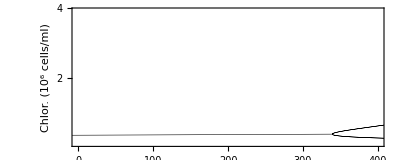

```mathematica
bifPlot=ListLinePlot[bifPtsChlorScaled,
PlotStyle->Table[{Black,Thickness[ltb]},{i,1,Length[bifPtsChlor]}],
LabelStyle->ls,
InterpolationOrder->1,
PlotRange->{{0,400},All},
Frame->True,
FrameLabel->{{"Chlor. (10^6 cells/ml)",Style["Brach. (females/ml)",White]},{"",""}},
FrameTicks->{{Transpose[{Range[-4/40,6],Range[0,6]}],None},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->0.4]
```

### Bifurcation trajectory

```mathematica
bTicks=Range[bl,bh,0.02];
bTicksT=(bTicks-bl)*tmax/(bh-bl);
```

```mathematica
plotX
```

-Graphics-

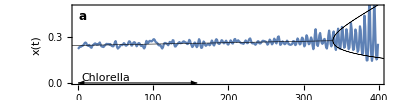

```mathematica
plotBifTraj=Show[{plotX,bifPlot},
PlotRange->{{0,tmax},{0,0.5}},
ImageSize->imgs,
LabelStyle->ls,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Dilution rate, δ"}},
AspectRatio->aRatio,
Axes->False,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{bTicksT,bTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Chlorella",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Arrowheads[{-aHeadSize,aHeadSize}*0.7],
Thickness[0.002],
Arrow[{Scaled[{0,0.2},{0,0}],Scaled[{0,0.2},{windowComps*dt2,0}]}]
}
]
```

## EWS Plots

### Variance

```mathematica
colVar=TMBcolours[[2]];
```

```mathematica
indexEws=Position[ewsSingles[[1]],"Variance"][[1,1]];
```

```mathematica
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,Smax,AIC fold,AIC hopf,AIC null,Params fold,Params flip,Params hopf,Params null}

```mathematica
(* Obtain values *)
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,indexEws}]],
{i,stateVar,_,_}]⟦;;,{3,4}⟧,
{i,1,numEws}];
```

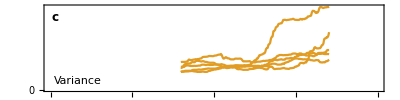

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=-0.00005;
ymax=0.001;
plotVar=ListLinePlot[series,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
PlotRange->{{0,tmax},All},
PlotStyle->colVar,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[0,20,5],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Smax

```mathematica
colSmax=TMBcolours[[3]];
```

```mathematica
indexEws=Position[ewsSingles[[1]],"Smax"][[1,1]];
```

```mathematica
(* Obtain values *)
series=Table[
Cases[
ewsSingles[[2;;,{1,2,3,indexEws}]],
{i,stateVar,_,p_/;UnsameQ[p,""]}]⟦;;,{3,4}⟧,
{i,1,numEws}];
```

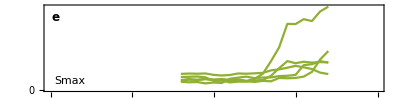

```mathematica
(* Plot bootstrapped and standard EWS *)
ymin=-0.00003;
ymax=0.0002;
plotSmax=ListLinePlot[series,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
PlotStyle->colSmax,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Range[0,14,2],Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["e",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax",ls],textPos,{-1,0}]}]
```

### Autocorrelation combined

```mathematica
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,Smax,AIC fold,AIC hopf,AIC null,Params fold,Params flip,Params hopf,Params null}

```mathematica
(* figure colours *)
acCols=TMBcolours[[{4,5,7}]]
```

{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.363898, 0.618501, 0.782349]}

```mathematica
indexEws=Position[ewsSingles[[1]],#][[1,1]]&/@{"Lag-1 AC","Lag-3 AC","Lag-6 AC"};
```

```mathematica
indexEws
```

{9,10,11}

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,Join[{1,2,3},indexEws]]],
{i,stateVar,_,_,_,_}]⟦;;,{3,j}⟧,
{i,1,numEws},{j,{4,5,6}}];
```

```mathematica
series2=Flatten[series,1];
```

```mathematica
(* line legend *)
legend=LineLegend[acCols,Table["lag-"<>ToString[i],{i,{1,3,6}}],Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
Table[Table[acCols[[j]],{i,1,numEws}],{j,1,3}]
```

{{RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.922526, 0.385626, 0.209179]},{RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.528488, 0.470624, 0.701351]},{RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[0.363898, 0.618501, 0.782349]}}

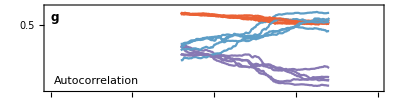

```mathematica
ymin=-1;
ymax=1;
plotAC=ListLinePlot[series2,
Joined->True,
Axes->False,
LabelStyle->ls,
Frame->True,
FrameTicks->{{Range[-1,1,0.5],Automatic},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
PlotRange->{{0,tmax},{-0.9,0.9}},
PlotStyle->Table[Table[acCols[[j]],{i,1,numEws}],{j,1,3}],
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotLegends->Placed[legend,{0.15,0.65}],
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
Text[Style["Autocorrelation",ls],Scaled[{0.03,0.12}],{-1,0}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin(* yorigin value *)}],Scaled[{0,arHeight},{windowComps*dt2,ymin (* yorigin value *)}]}]*)
Text[Style["g",labelLetterPosSize,Bold],labelLetterPos]}]
```

### AIC

```mathematica
ewsSingles[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-3 AC,Lag-6 AC,Coefficient of variation,Skewness,Kurtosis,Smax,AIC fold,AIC hopf,AIC null,Params fold,Params flip,Params hopf,Params null}

```mathematica
(* figure colours *)
aicCols=TMBcolours[[{15,8,6}]]
```

{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[1, 0.75, 0],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
indexEws=Position[ewsSingles[[1]],#][[1,1]]&/@{"AIC fold","AIC hopf", "AIC null"};
```

```mathematica
series=Table[
Cases[
ewsSingles[[2;;,Join[{1,2,3},indexEws]]],
{i,stateVar,_,_Real,_Real,_Real}]⟦;;,{3,j}⟧,
{i,1,numEws},{j,{4,5,6}}];
```

```mathematica
series//Dimensions
```

{5,3,19,2}

```mathematica
series2=Flatten[series,1];
```

```mathematica
(* line legend *)
legend=LineLegend[aicCols,{"w_fold","w_hopf","w_null"},Spacings->{0,0.2},LabelStyle->(ls-1)]
```

```mathematica
Flatten[Table[Table[aicCols[[j]],{i,1,numEws}],{j,1,3}]]
```

{RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965],RGBColor[1, 0.75, 0],RGBColor[1, 0.75, 0],RGBColor[1, 0.75, 0],RGBColor[1, 0.75, 0],RGBColor[1, 0.75, 0],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.772079, 0.431554, 0.102387]}

```mathematica
series2//Dimensions
```

{15,19,2}

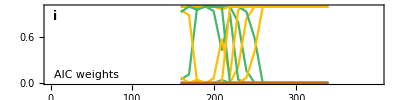

```mathematica
(* All AIC weights on one plot *)
ymin=-0.05;
ymax=1.07;
plotAIC=ListLinePlot[series2,
LabelStyle->ls,
Frame->True,
FrameLabel->{{"",""},{"Time (days)",""}},
FrameTicks->{{Automatic,Automatic},{Range[0,tmax,50],Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRange->{{0,tmax},All},
AxesOrigin->{0,0},
ImagePadding->{{padLeft,padRight},{40,padTop}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotStyle->Table[Table[aicCols[[j]],{i,1,numEws}],{j,1,3}],
PlotLegends->Placed[legend,{0.15,0.65}],
Epilog->{Directive[{Black}],
Text[Style["AIC weights",ls],Scaled[{0.03,0.12}],{-1,0}],
Text[Style["i",labelLetterPosSize,Bold],labelLetterPos]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

```mathematica
ktauData//Dimensions
```

{11,12}

```mathematica
ktauData[[1]]
```

{Realisation number,Variable,index,Lag-3 AC,Lag-6 AC,Smax,Standard deviation,Lag-1 AC,Coefficient of variation,Variance,Skewness,Kurtosis}

```mathematica
(* select values csp to state variable of choice *)
ktauValsState=Cases[ktauData,Join[{_,stateVar},Table[_,{i,1,Dimensions[ktauData][[2]]-2}]]];
```

### Variance

```mathematica
index=Position[ktauData[[1]],"Variance"][[1,1]];
```

```mathematica
ktauVals=ktauValsState[[;;,index]];
```

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[{ktauVals,ktauVals,ktauVals},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colVar,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
index=Position[ktauData[[1]],"Smax"][[1,1]];
```

```mathematica
ktauVals=ktauValsState[[;;,index]];
```

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[{ktauVals,ktauVals,ktauVals},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->{Opacity[0],colSmax,Opacity[0]},
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["f",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Autocorrelation

```mathematica
index=Table[Position[ktauData[[1]],label],{label,{"Lag-1 AC","Lag-2 AC", "Lag-10 AC"}}]//Flatten
```

{8}

```mathematica
ktauVals=ktauValsState[[;;,index]]//Transpose;
```

```mathematica
(* Box plot *)
boxAc=BoxWhiskerChart[ktauVals,If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->acCols,
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["h",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### AIC weights - take ensemble of values at time 300

```mathematica
aicData[[1]]
```

{Realisation number,Variable,AIC fold,AIC hopf,AIC null}

```mathematica
aicFold=Cases[aicData,{_,stateVar,_,_,_}][[2;;,3]];
aicHopf=Cases[aicData,{_,stateVar,_,_,_}][[2;;,4]];
aicNull=Cases[aicData,{_,stateVar,_,_,_}][[2;;,5]];
```

```mathematica
(* Box plot *)
boxAic=BoxWhiskerChart[{aicFold,aicHopf,aicNull},If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{0,1},
ImageSize->imgsBox,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.25]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->aicCols,
ImagePadding->padBox,
Epilog->{
Text[Style["t=300",ls],ktauTextPos,{-1,0}],
Text[Style["j",labelLetterPosSize,Bold],labelLetterPosBox]}
]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Power Spectrum

```mathematica
plotNum=4;
```

```mathematica
specSingles//Dimensions
```

{7791,5}

```mathematica
(* Obtain pspec data for plot_num *)
specData=Cases[specSingles,
{plotNum,stateVar,_,_,_}][[;;,{3,4,5}]];
```

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[specData[[;;,1]]][[1;;;;6]]
```

{159.,219.,279.,339.}

```mathematica
(* Organise list of power spectra to plot *)
specsPlot=Table[
Cases[specData,
{i,_,_}]⟦;;,{2,3}⟧,
{i,plotTimes}];
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
plotTimesUnit
```

{0.,0.333333,0.666667,1.}

```mathematica
(* create a color legend that spans range of times *)
timeRange=plotTimes[[{1,-1}]];
colLegend=BarLegend[{colFun1[(#-199)/(419-199)]&,timeRange},LegendLabel->"Time",LegendMarkerSize->150]
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

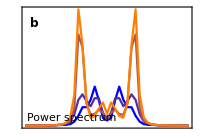

```mathematica
ymin=-0.5;
ymax=3;
plotPspec=ListLinePlot[specsPlot,
PlotRange->{{-Pi,Pi},All},
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
(*PlotRangeClipping->False,*)
FrameTicks->{{None,Range[0,1,0.02]},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.6,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.3cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAIC,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAic,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotAC,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxAc,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotSmax,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmax,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotBifTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspec,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

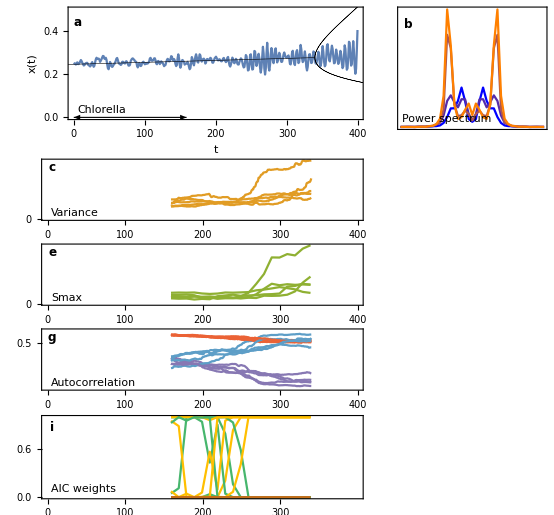

```mathematica
plotGrid
```

```mathematica
(*Export["figures/flip_sub_ews.png",plotGrid,ImageResolution->400];*)
```